# Contour Plot Demo

## Contour Plot

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sanchez.hmsc/Documents/GitHub/dataViz_CADi/Day01/scripts

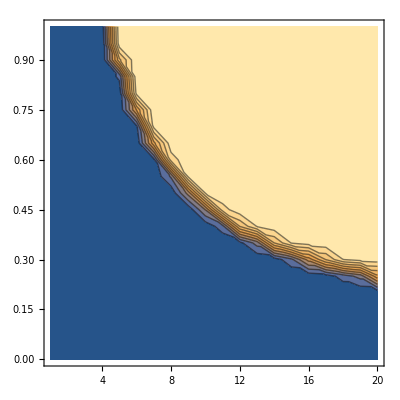

```mathematica
filteredData=Import["factorialData.csv"];
ListContourPlot[filteredData]
```

```mathematica
ListContourPlot[filteredData
,FrameStyle->Thick
,FrameTicksStyle->Directive[Black,15]
]
```

-Graphics-

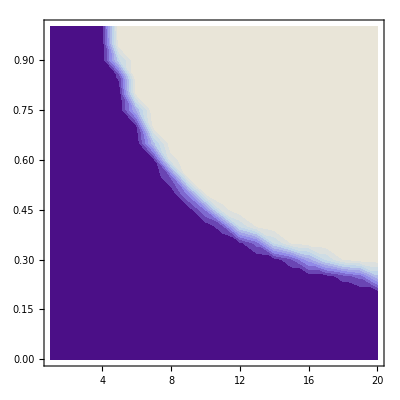

```mathematica
ListContourPlot[filteredData
,ColorFunction->"LakeColors"
,ContourStyle->None
,FrameStyle->Thick
,FrameTicksStyle->Directive[Black,15]
]
```

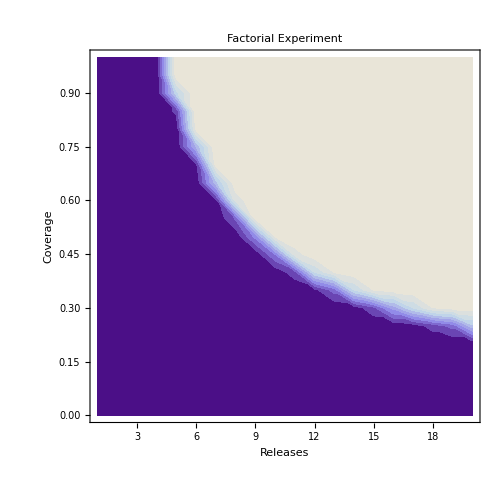

```mathematica
c1=ListContourPlot[filteredData
,ColorFunction->"LakeColors"
,ContourStyle->None
,FrameLabel->(Style[#,20]&/@{"Releases","Coverage"})
,FrameStyle->Thick
,FrameTicksStyle->Directive[Black,15]
,ImageSize->500
,PlotLabel->Style["Factorial Experiment",Black,30]
,PlotRangePadding->0
]
```

## 3D Plot

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sanchez.hmsc/Desktop

```mathematica
filteredData=Import["filteredData.csv"];
ListPlot3D[filteredData]
```

-Graphics3D-

```mathematica
ListPlot3D[filteredData
,AxesStyle->Directive[15]
,BoxStyle->Directive[Thick,Opacity[.25]]
]
```

-Graphics3D-

```mathematica
ListPlot3D[filteredData
,AxesStyle->Directive[15]
,BoxStyle->Directive[Thick,Opacity[1]]
,ColorFunction->"LakeColors"
]
```

-Graphics3D-

```mathematica
ListPlot3D[filteredData
,AxesLabel->(Style[#,20]&/@{"Releases","Coverage"})
,AxesStyle->Directive[15]
,BoxStyle->Directive[Thick,Opacity[1]]
,ColorFunction->"LakeColors"
,PlotLabel->Style["Factorial Experiment",Black,30]
,PlotRangePadding->0
]
```

-Graphics3D-

```mathematica
c2=ListPlot3D[filteredData
,AxesLabel->(Style[#,20]&/@{"Releases","Coverage"})
,AxesStyle->Directive[15]
,BoxStyle->Directive[Thick,Opacity[1]]
,ColorFunction->"LakeColors"
,ImageSize->750
,InterpolationOrder->0
,Mesh->None
,PlotLabel->Style["Factorial Experiment",Black,30]
,PlotRangePadding->0
]
```

-Graphics3D-

## Both

```mathematica
GraphicsGrid[{{c1,c2}}]
```

-Graphics-